## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="TKT1";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp3.csv";

mainFolder = "fit_TKT1_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{r5p,Null;xu5p__D,Null,Keq substrate}

{4.72,Keq value}

{r5p,Km or S05 substrate}

{0.0014,Km or S05 value}

(r5p^c+xu5p__D^c⇌g3p^c+s7p^c)^TKT1

Ping Pong Bi Bi; xu5p-D,g3p,r5p,s7p

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p,Null;xu5p__D,Null | 4.72 | 4.484
4.956 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p | 0.0014 | 0.00133
0.00147 | xu5p__D | 0.016
thmpp | 0.001 | M | 8.5 | 30 | glygly | 0.05 | mg2 | 0.005
cl | 0.01

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities ={1};
kmPriorities = {1};
s05Priorities = Null;
kcatPriorities = Null;
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(r5p^c+xu5p__D^c⇌g3p^c+s7p^c)^TKT1

Ping Pong Bi Bi; xu5p-D,g3p,r5p,s7p

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p,Null;xu5p__D,Null | 4.72 | 4.484
4.956 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | r5p | 0.0014 | 0.00133
0.00147 | xu5p__D | 0.016
thmpp | 0.001 | M | 8.5 | 30 | glygly | 0.05 | mg2 | 0.005
cl | 0.01

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_TKT1[c] + xu5p__D[c] <=> E_TKT1[c]&xu5p__D",
				"E_TKT1[c]&xu5p__D <=> E_TKT1[c]&mod&g3p",
				"E_TKT1[c]&mod&g3p <=> E_TKT1[c]&mod + g3p[c]",

				"E_TKT1[c]&mod + r5p[c] <=> E_TKT1[c]&mod&r5p",
				"E_TKT1[c]&mod&r5p <=> E_TKT1[c]&s7p",
				"E_TKT1[c]&s7p <=> E_TKT1[c] + s7p[c]"};

enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((TKT1^c)_^+xu5p__D^c⇌(TKT1^c&xu5p_^D)_^)^TKT11,((TKT1^c&s7p^c)_^⇌(TKT1^c)_^+s7p^c)^TKT12,((TKT1^c&mod^c)_^+r5p^c⇌(TKT1^c&mod^c&r5p^c)_^)^TKT13,((TKT1^c&xu5p_^D)_^⇌(TKT1^c&mod^c&g3p^c)_^)^TKT14,((TKT1^c&mod^c&r5p^c)_^⇌(TKT1^c&s7p^c)_^)^TKT15,((TKT1^c&mod^c&g3p^c)_^⇌(TKT1^c&mod^c)_^+g3p^c)^TKT16}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((TKT1^c)_^+xu5p__D^c⇌(TKT1^c&xu5p_^D)_^)^TKT11,Overscript[(TKT1^c&s7p^c)_^⇌(TKT1^c)_^+s7p^c, TKT12],((TKT1^c&mod^c)_^+r5p^c⇌(TKT1^c&mod^c&r5p^c)_^)^TKT13,((TKT1^c&xu5p_^D)_^⇌(TKT1^c&mod^c&g3p^c)_^)^TKT14,((TKT1^c&mod^c&r5p^c)_^⇌(TKT1^c&s7p^c)_^)^TKT15,Overscript[(TKT1^c&mod^c&g3p^c)_^⇌(TKT1^c&mod^c)_^+g3p^c, TKT16]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

{r5p^c→0,xu5p__D^c→0}

{g3p^c→0,s7p^c→0}

{r5p^c→∞,xu5p__D^c→∞}

{g3p^c→∞,s7p^c→∞}

Added inhibition reactions:

{}

Generating flux equation...

{((TKT1^c&xu5p_^D)_^-((TKT1^c&mod^c&g3p^c)_^)/K_TKT14) Volume_c k_TKT14^⟶,((TKT1^c&mod^c&r5p^c)_^-((TKT1^c&s7p^c)_^)/K_TKT15) Volume_c k_TKT15^⟶}

Volume_c (-(TKT1^c&mod^c&g3p^c)_^ k_TKT14^⟵+(TKT1^c&xu5p_^D)_^ k_TKT14^⟶-(TKT1^c&s7p^c)_^ k_TKT15^⟵+(TKT1^c&mod^c&r5p^c)_^ k_TKT15^⟶)

1

2

3

1.30081

4

0.00169

5

0.00027

Simplifying...

6

0.511223

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

```mathematica
FilePrint@dataPathList
```

Priority	g3p[c]	r5p[c]	s7p[c]	xu5p__D[c]	param_TKT1_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt"	4.72
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt"	4.72
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt"	4.72
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt"	4.72
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt"	4.72
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt"	4.72
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt"	4.72
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt"	4.72
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt"	4.72
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt"	4.72
1	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt"	4.72
1	0	0.00014000000000000004	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt"	0.09090909090909093
1	0	0.00022188504694455605	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt"	0.13680688860321008
1	0	0.00035166410041134126	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt"	0.20076000891310175
1	0	0.0005573500387748965	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt"	0.2847472489508015
1	0	0.0008833402822722705	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt"	0.3868631798468569
1	0	0.0014000000000000004	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt"	0.5000000000000001
1	0	0.0022188504694455606	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt"	0.6131368201531432
1	0	0.0035166410041134162	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt"	0.7152527510491987
1	0	0.005573500387748964	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt"	0.7992399910868982
1	0	0.008833402822722705	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt"	0.86319311139679
1	0	0.014000000000000005	0	0.016	1	8.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt"	0.9090909090909092

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_xu5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateRev_s7p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_xu5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateRev_s7p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 0.584926299039
best_fit: 0.636719929114
best_fit: 0.54024653143
best_fit: 0.777523760162
best_fit: 0.482561838646

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 8.69305×10^-14 | 7.55691×10^-27 | 9.44134×10^-13 | 2.00028×10^-11 | 4.72 | 4.72
1 | haldaneRatio_1 | 8.69305×10^-14 | 7.55691×10^-27 | 9.44134×10^-13 | 2.00028×10^-11 | 4.72 | 4.72
1 | haldaneRatio_1 | 8.69305×10^-14 | 7.55691×10^-27 | 9.44134×10^-13 | 2.00028×10^-11 | 4.72 | 4.72
1 | haldaneRatio_1 | 8.69305×10^-14 | 7.55691×10^-27 | 9.44134×10^-13 | 2.00028×10^-11 | 4.72 | 4.72
1 | haldaneRatio_1 | 8.69305×10^-14 | 7.55691×10^-27 | 9.44134×10^-13 | 2.00028×10^-11 | 4.72 | 4.72
1 | haldaneRatio_1 | 8.69305×10^-14 | 7.55691×10^-27 | 9.44134×10^-13 | 2.00028×10^-11 | 4.72 | 4.72
1 | haldaneRatio_1 | 8.69305×10^-14 | 7.55691×10^-27 | 9.44134×10^-13 | 2.00028×10^-11 | 4.72 | 4.72
1 | haldaneRatio_1 | 8.69305×10^-14 | 7.55691×10^-27 | 9.44134×10^-13 | 2.00028×10^-11 | 4.72 | 4.72
1 | haldaneRatio_1 | 8.69305×10^-14 | 7.55691×10^-27 | 9.44134×10^-13 | 2.00028×10^-11 | 4.72 | 4.72
1 | haldaneRatio_1 | 8.69305×10^-14 | 7.55691×10^-27 | 9.44134×10^-13 | 2.00028×10^-11 | 4.72 | 4.72
1 | haldaneRatio_1 | 8.69305×10^-14 | 7.55691×10^-27 | 9.44134×10^-13 | 2.00028×10^-11 | 4.72 | 4.72
1 | relRateFor_r5p | 5.98566×10^-12 | 3.58281×10^-23 | 1.25296×10^-12 | 1.37825×10^-9 | 0.0909091 | 0.0909091
1 | relRateFor_r5p | 5.68356×10^-12 | 3.23029×10^-23 | 1.79037×10^-12 | 1.30869×10^-9 | 0.136807 | 0.136807
1 | relRateFor_r5p | 5.26235×10^-12 | 2.76923×10^-23 | 2.43261×10^-12 | 1.2117×10^-9 | 0.20076 | 0.20076
1 | relRateFor_r5p | 4.70946×10^-12 | 2.2179×10^-23 | 3.08775×10^-12 | 1.08438×10^-9 | 0.284747 | 0.284747
1 | relRateFor_r5p | 4.03705×10^-12 | 1.62978×10^-23 | 3.59612×10^-12 | 9.29559×10^-10 | 0.386863 | 0.386863
1 | relRateFor_r5p | 3.29214×10^-12 | 1.08382×10^-23 | 3.79019×10^-12 | 7.58038×10^-10 | 0.5 | 0.5
1 | relRateFor_r5p | 2.5471×10^-12 | 6.48773×10^-24 | 3.59601×10^-12 | 5.86494×10^-10 | 0.613137 | 0.613137
1 | relRateFor_r5p | 1.87478×10^-12 | 3.51479×10^-24 | 3.08764×10^-12 | 4.31685×10^-10 | 0.715253 | 0.715253
1 | relRateFor_r5p | 1.32185×10^-12 | 1.74728×10^-24 | 2.43261×10^-12 | 3.04365×10^-10 | 0.79924 | 0.79924
1 | relRateFor_r5p | 9.00766×10^-13 | 8.11379×10^-25 | 1.79035×10^-12 | 2.0741×10^-10 | 0.863193 | 0.863193
1 | relRateFor_r5p | 5.98591×10^-13 | 3.58311×10^-25 | 1.253×10^-12 | 1.3783×10^-10 | 0.909091 | 0.909091

### Simulated Data and Best Fit Data Plot

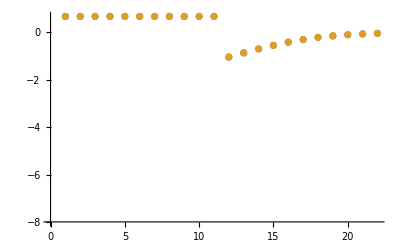

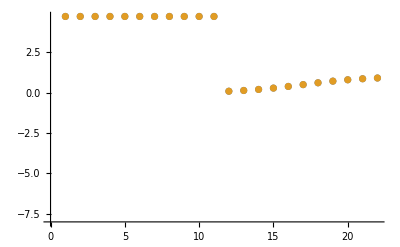

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

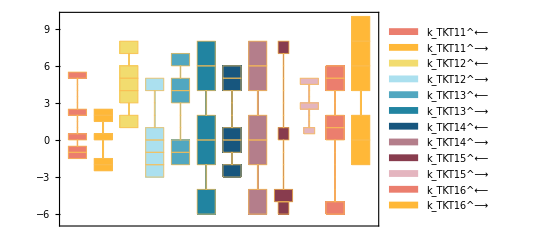

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

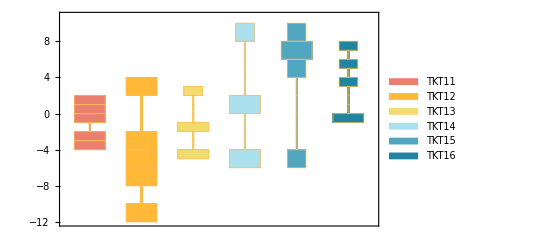

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

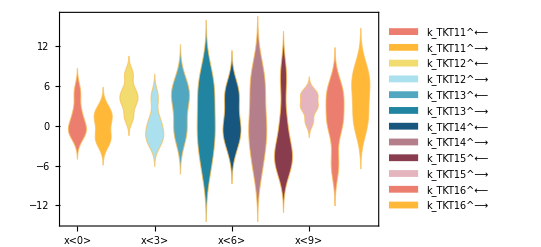

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

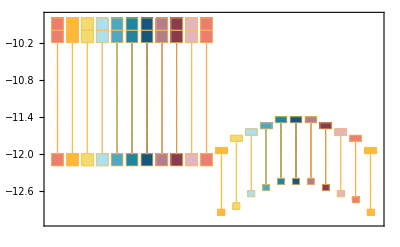

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

backCalculateKms[(r5p^c+xu5p__D^c⇌g3p^c+s7p^c)^TKT1,{{1,r5p,0.0014,{0.00133,0.00147},{{xu5p__D,0.016},{thmpp,0.001}},M,8.5,30,{{glygly,0.05}},{{mg2,0.005},{cl,0.01}}}},{(r5p^c k_TKT13^⟶ (k_TKT12^⟶ k_TKT14^⟶ k_TKT15^⟶ k_TKT16^⟶+k_TKT11^⟵ k_TKT12^⟶ k_TKT15^⟶ (k_TKT14^⟵+k_TKT16^⟶)+xu5p__D^c k_TKT11^⟶ (k_TKT14^⟶ (k_TKT15^⟵+k_TKT15^⟶) k_TKT16^⟶+k_TKT12^⟶ (k_TKT14^⟵ k_TKT15^⟶+k_TKT15^⟶ k_TKT16^⟶+k_TKT14^⟶ (k_TKT15^⟶+k_TKT16^⟶)))))/(xu5p__D^c k_TKT11^⟶ k_TKT14^⟶ (k_TKT13^⟵ k_TKT15^⟵+k_TKT12^⟶ (k_TKT13^⟵+k_TKT15^⟶)) k_TKT16^⟶+r5p^c k_TKT13^⟶ (k_TKT12^⟶ k_TKT14^⟶ k_TKT15^⟶ k_TKT16^⟶+k_TKT11^⟵ k_TKT12^⟶ k_TKT15^⟶ (k_TKT14^⟵+k_TKT16^⟶)+xu5p__D^c k_TKT11^⟶ (k_TKT14^⟶ (k_TKT15^⟵+k_TKT15^⟶) k_TKT16^⟶+k_TKT12^⟶ (k_TKT14^⟵ k_TKT15^⟶+k_TKT15^⟶ k_TKT16^⟶+k_TKT14^⟶ (k_TKT15^⟶+k_TKT16^⟶))))),(xu5p__D^c k_TKT11^⟶ (k_TKT14^⟶ (k_TKT13^⟵ k_TKT15^⟵+k_TKT12^⟶ (k_TKT13^⟵+k_TKT15^⟶)) k_TKT16^⟶+r5p^c k_TKT13^⟶ (k_TKT14^⟶ (k_TKT15^⟵+k_TKT15^⟶) k_TKT16^⟶+k_TKT12^⟶ (k_TKT14^⟵ k_TKT15^⟶+k_TKT15^⟶ k_TKT16^⟶+k_TKT14^⟶ (k_TKT15^⟶+k_TKT16^⟶)))))/(xu5p__D^c k_TKT11^⟶ k_TKT14^⟶ (k_TKT13^⟵ k_TKT15^⟵+k_TKT12^⟶ (k_TKT13^⟵+k_TKT15^⟶)) k_TKT16^⟶+r5p^c k_TKT13^⟶ (k_TKT12^⟶ k_TKT14^⟶ k_TKT15^⟶ k_TKT16^⟶+k_TKT11^⟵ k_TKT12^⟶ k_TKT15^⟶ (k_TKT14^⟵+k_TKT16^⟶)+xu5p__D^c k_TKT11^⟶ (k_TKT14^⟶ (k_TKT15^⟵+k_TKT15^⟶) k_TKT16^⟶+k_TKT12^⟶ (k_TKT14^⟵ k_TKT15^⟶+k_TKT15^⟶ k_TKT16^⟶+k_TKT14^⟶ (k_TKT15^⟶+k_TKT16^⟶)))))},{(g3p^c (k_TKT11^⟵ k_TKT14^⟵ (k_TKT13^⟵ k_TKT15^⟵+k_TKT12^⟶ (k_TKT13^⟵+k_TKT15^⟶))+s7p^c k_TKT12^⟵ (k_TKT13^⟵ (k_TKT14^⟵+k_TKT14^⟶) k_TKT15^⟵+k_TKT11^⟵ k_TKT13^⟵ (k_TKT14^⟵+k_TKT15^⟵)+k_TKT11^⟵ k_TKT14^⟵ (k_TKT15^⟵+k_TKT15^⟶))) k_TKT16^⟵)/(g3p^c k_TKT11^⟵ k_TKT14^⟵ (k_TKT13^⟵ k_TKT15^⟵+k_TKT12^⟶ (k_TKT13^⟵+k_TKT15^⟶)) k_TKT16^⟵+s7p^c k_TKT12^⟵ (g3p^c k_TKT13^⟵ (k_TKT14^⟵+k_TKT14^⟶) k_TKT15^⟵ k_TKT16^⟵+g3p^c k_TKT11^⟵ k_TKT14^⟵ (k_TKT15^⟵+k_TKT15^⟶) k_TKT16^⟵+k_TKT13^⟵ k_TKT14^⟶ k_TKT15^⟵ k_TKT16^⟶+k_TKT11^⟵ k_TKT13^⟵ (k_TKT14^⟵ (k_TKT15^⟵+g3p^c k_TKT16^⟵)+k_TKT15^⟵ (g3p^c k_TKT16^⟵+k_TKT16^⟶)))),(s7p^c k_TKT12^⟵ (g3p^c k_TKT13^⟵ (k_TKT14^⟵+k_TKT14^⟶) k_TKT15^⟵ k_TKT16^⟵+g3p^c k_TKT11^⟵ k_TKT14^⟵ (k_TKT15^⟵+k_TKT15^⟶) k_TKT16^⟵+k_TKT13^⟵ k_TKT14^⟶ k_TKT15^⟵ k_TKT16^⟶+k_TKT11^⟵ k_TKT13^⟵ (k_TKT14^⟵ (k_TKT15^⟵+g3p^c k_TKT16^⟵)+k_TKT15^⟵ (g3p^c k_TKT16^⟵+k_TKT16^⟶))))/(g3p^c k_TKT11^⟵ k_TKT14^⟵ (k_TKT13^⟵ k_TKT15^⟵+k_TKT12^⟶ (k_TKT13^⟵+k_TKT15^⟶)) k_TKT16^⟵+s7p^c k_TKT12^⟵ (g3p^c k_TKT13^⟵ (k_TKT14^⟵+k_TKT14^⟶) k_TKT15^⟵ k_TKT16^⟵+g3p^c k_TKT11^⟵ k_TKT14^⟵ (k_TKT15^⟵+k_TKT15^⟶) k_TKT16^⟵+k_TKT13^⟵ k_TKT14^⟶ k_TKT15^⟵ k_TKT16^⟶+k_TKT11^⟵ k_TKT13^⟵ (k_TKT14^⟵ (k_TKT15^⟵+g3p^c k_TKT16^⟵)+k_TKT15^⟵ (g3p^c k_TKT16^⟵+k_TKT16^⟶))))},{r5p^c→∞,xu5p__D^c→∞},{g3p^c→∞,s7p^c→∞},{k_TKT11^⟵→0.0563762,k_TKT11^⟶→0.00720942,k_TKT12^⟵→2359.82,k_TKT12^⟶→9.97278,k_TKT13^⟵→0.0358971,k_TKT13^⟶→2.28724×10^-6,k_TKT14^⟵→1.59484,k_TKT14^⟶→1.6102×10^-6,k_TKT15^⟵→1.21757×10^-6,k_TKT15^⟶→4.42575,k_TKT16^⟵→1.21715×10^-6,k_TKT16^⟶→45.4609},1,TKT1]

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
4.72 | 4.72 | 4.41022×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
4.72 | 4.72 | 4.41022×10^-10

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKic[{{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0.00014,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.0909091},{1,0,0.000221885,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.136807},{1,0,0.000351664,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.20076},{1,0,0.00055735,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.284747},{1,0,0.00088334,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.386863},{1,0,0.0014,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.5},{1,0,0.00221885,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.613137},{1,0,0.00351664,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.715253},{1,0,0.0055735,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.79924},{1,0,0.0088334,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.863193},{1,0,0.014,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.909091}},{4.33257×10^-23,{0.00793658,5.68819,1.25012×10^-6,7.9809×10^8,8.6921×10^8,41.2655,3.92843,0.0000294543,3.87462×10^7,7.97242×10^8,2.2553×10^6,3.17651},{4.72,4.72,4.72,4.72,4.72,4.72,4.72,4.72,4.72,4.72,4.72,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091}},{Priority,g3p[c],r5p[c],s7p[c],xu5p-D[c],param_TKT1_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKiu[{{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/haldaneRatio_1.txt,4.72},{1,0,0.00014,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.0909091},{1,0,0.000221885,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.136807},{1,0,0.000351664,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.20076},{1,0,0.00055735,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.284747},{1,0,0.00088334,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.386863},{1,0,0.0014,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.5},{1,0,0.00221885,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.613137},{1,0,0.00351664,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.715253},{1,0,0.0055735,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.79924},{1,0,0.0088334,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.863193},{1,0,0.014,0,0,1,8.5,30,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_TKT1_typeII/input/relRateFor_r5p.txt,0.909091}},{4.33257×10^-23,{0.00793658,5.68819,1.25012×10^-6,7.9809×10^8,8.6921×10^8,41.2655,3.92843,0.0000294543,3.87462×10^7,7.97242×10^8,2.2553×10^6,3.17651},{4.72,4.72,4.72,4.72,4.72,4.72,4.72,4.72,4.72,4.72,4.72,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091}},{Priority,g3p[c],r5p[c],s7p[c],xu5p-D[c],param_TKT1_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Set::shape: Lists {predictedParameters,predictedParameterErrors} and exportPredictedParametersAndErrors[(atp^c+skm^c⇌adp^c+skm5p^c)^SHKK,SHKK,«20»,{Priority,adp[c],atp[c],skm[c],skm5p[c],param_SHKK_total,param_pH,param_Temp,FileFlag,Target_Data}] are not the same shape.

Part::take: Cannot take positions 3 through -1 in predictedParameterErrors.

Part::partd: Part specification predictedParameterErrors⟦1⟧ is longer than depth of object.

BoxWhiskerChart::ldata: Transpose[predictedParameterErrors⟦3;;All⟧] is not a valid dataset or list of datasets.

BoxWhiskerChart[Transpose[predictedParameterErrors⟦3;;All⟧],ChartLabels→{predictedParameterErrors⟦1⟧}]